## Training set

### Wikipedia

```mathematica
fractalData
```

<|-Graphics-→0.6309,-Graphics-→1,-Graphics-→1.0812,-Graphics-→1.0933,-Graphics-→1.12915,-Graphics-→1.2,-Graphics-→1.2083,-Graphics-→1.2108,-Graphics-→1.2619,-Graphics-→1.2619,-Graphics-→1.2619,-Graphics-→1.2683,-Graphics-→1.328,-Graphics-→1.3057,-Graphics-→1.3934,-Graphics-→1.4649,-Graphics-→1.4649,-Graphics-→1.5,-Graphics-→1.5,-Graphics-→1.5236,-Graphics-→1.5849,-Graphics-→1.61803,-Graphics-→1.6379,-Graphics-→1.6667,-Graphics-→1.7,-Graphics-→1.7227,-Graphics-→1.7712,-Graphics-→1.7848,-Graphics-→1.8687,-Graphics-→1.8617,-Graphics-→1.8928,-Graphics-→1.974,-Graphics-→1.934|>

### Random Julia set

```mathematica
juliaFractals=CreateJuliaFractals[100];
```

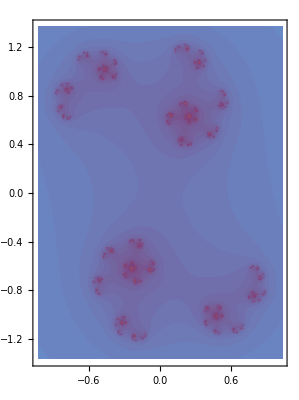
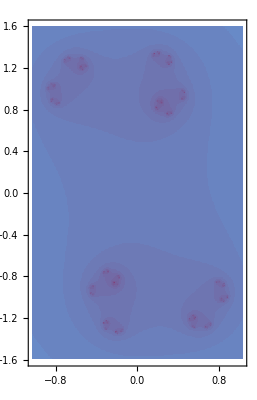
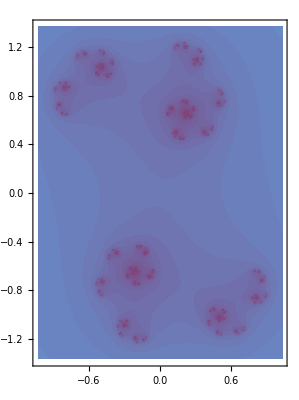
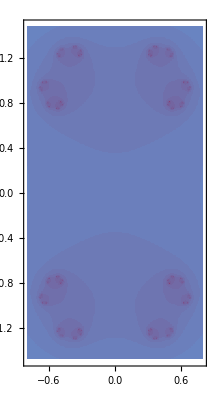
<|-Graphics-→1.00213,-Graphics-→1.00915,-Graphics-→1.00117,-Graphics-→1.07497,-Graphics-→1.18588,-Graphics-→1.08533,-Graphics-→1.00754,-Graphics-→1.13982,-Graphics-→1.11971,-Graphics-→1.002|>

```mathematica
RandomSample[juliaFractals,10]
```

## Tests

```mathematica
PredictFractalDimension[fractalData∪juliaFractals,5]
```

{-Graphics-→{1.00022,1.29943},-Graphics-→{1.04314,1.30814},-Graphics-→{1.04596,1.37036},-Graphics-→{1.07945,1.19648},-Graphics-→{1.02535,1.32383}}